# David Meretzky 785 Homework 3 FEM

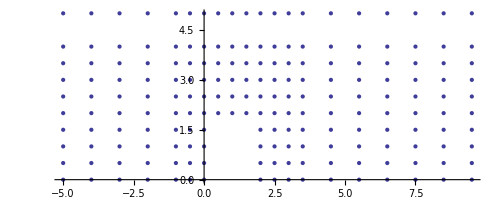

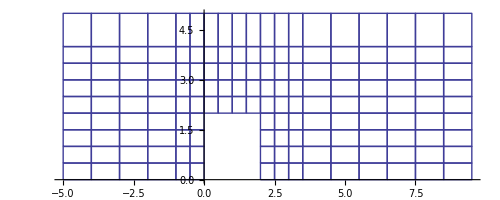

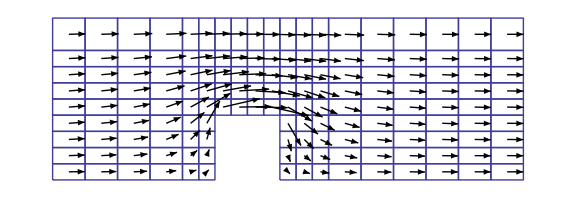

```mathematica
(*Parameters*)


nodes = Import["/Users/David/Downloads/ChnlNodes.dat"];
elements = Import["/Users/David/Downloads/ChnlElems.dat"];

el= {};
For[i = 1, i ≤  155, i++,
node = nodes[[elements[[i,2;;5]],2;;3]];
 AppendTo[node,nodes[[elements[[i,2;;5]],2;;3]][[1]]];
AppendTo[el,node];
];

ListPlot[nodes[[1;;188,2;;3]], AspectRatio->Automatic]
ListLinePlot[el, PlotStyle->Hue[.67, .6, .6], AspectRatio->Automatic]

n1[α_,β_,γ_,δ_,x_,y_] = (((γ - x)*(δ - y))/((γ - α)*(δ-β)));
n2[α_,β_,γ_,δ_,x_,y_] = (((x - α)*(δ - y))/((γ - α)*(δ-β)));
n3[α_,β_,γ_,δ_,x_,y_] = (((x - α)*(y - β))/((γ - α)*(δ-β)));n4[α_,β_,γ_,δ_,x_,y_] = (((γ - x)*(y - β))/((γ - α)*(δ-β)));

(*Making the K nxn matrix with Gaussian Quadrature*)
knByn = ConstantArray[0,{188,188}];

For[i = 1, i ≤ 155, ++i, 

element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[2]];
δ = nodes[[element[[2;;5]]]][[3]][[3]];
(*Print[n1[α,β,γ,δ,x,y]];
Print[n2[α,β,γ,δ,x,y]];
Print[n3[α,β,γ,δ,x,y]];
Print[n4[α,β,γ,δ,x,y]];*)

polynomials = {n1[α,β,γ,δ,x,y],n2[α,β,γ,δ,x,y],n3[α,β,γ,δ,x,y],n4[α,β,γ,δ,x,y]};

pointsx = {α + (γ-α)*(.5 - .5/Sqrt[3]),α + (γ-α)*(.5 + .5/Sqrt[3])};
pointsy = {β+ (δ-β)*(.5 - .5/Sqrt[3]),β+ (δ-β)*(.5 + .5/Sqrt[3])};


wx =.5*( γ - α);
wy =.5*(δ-β );

For[j = 1,j ≤ 4, j++, 

nj = element[[2;;5]][[j]];

js =  {D[polynomials[[j]],x],
D[polynomials[[j]],y]};

For[k =1, k ≤ 4, k ++, 

nk = element[[2;;5]][[k]];

ks = {D[polynomials[[k]],x],
D[polynomials[[k]],y]};

product =js.ks;


knByn[[nj,nk]] += ∑_(ys=1)^2 ∑_(xs=1)^2 wx*wy*(product /.x-> pointsx[[xs]]/.y->pointsy[[ys]]);
];
];
];


(*Making the R boundry vector using Gaussian Quadrature
*)
re = Range[188]-Range[188];

For[i = 1, i ≤155, i++, 
element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[2]];
δ = nodes[[element[[2;;5]]]][[3]][[3]];

polynomials = {n1[α,β,γ,δ,x,y],n2[α,β,γ,δ,x,y],n3[α,β,γ,δ,x,y],n4[α,β,γ,δ,x,y]};

pointsyinflow = {β+ (δ-β)*(.5 - .5/Sqrt[3]),β+ (δ-β)*(.5 + .5/Sqrt[3])};
pointsyoutflow = {β+ (δ-β)*(.5 - .5/Sqrt[3]),β+ (δ-β)*(.5 + .5/Sqrt[3])};

wy =.5*(δ-β );

If[i ≤ 9, 
upper = polynomials[[4]]/.x->α;
lower = polynomials[[1]]/.x->α;

re[[element[[5]]]]-=∑_(oned=1)^2 (wy*(upper/.y-> pointsyinflow[[oned]]));

re[[element[[2]]]]-=∑_(oned=1)^2 (wy*(lower/.y-> pointsyinflow[[oned]]));
];

If[i ≥ 147, 
upper = polynomials[[3]]/.x->γ;
lower = polynomials[[2]]/.x->γ;

re[[element[[4]]]]+=∑_(oned=1)^2 (wy*(upper/.y-> pointsyoutflow[[oned]]));

re[[element[[3]]]]+=∑_(oned=1)^2 (wy*(lower/.y-> pointsyoutflow[[oned]]));
];
];

(*Setting the unit vector at row 61 and solving for the coefficients*)

unit61 = Range[188]-Range[188];
unit61[[61]] = 1;
knByn[[61]] = unit61;

αe = LinearSolve[knByn,re];
flow = {};

(*Creating the flow field *)
For[i = 1, i ≤ 155, i++, 
element = elements[[i]];
α = nodes[[element[[2;;5]]]][[1]][[2]];
β = nodes[[element[[2;;5]]]][[1]][[3]];
γ = nodes[[element[[2;;5]]]][[3]][[2]];
δ = nodes[[element[[2;;5]]]][[3]][[3]];

coef = αe[[element[[2;;5]]]];

polynomials = {n1[α,β,γ,δ,x,y],n2[α,β,γ,δ,x,y],n3[α,β,γ,δ,x,y],n4[α,β,γ,δ,x,y]};

ϕ[x_,y_] = {D[coef.polynomials,x],D[coef.polynomials,y]};

centerx = .5*(γ-α) + α;
centery = .5*(δ-β) + β;
end =ϕ[centerx,centery];
arrow = Arrow[{{centerx,centery},{centerx,centery}+.5*end}];
AppendTo[flow, arrow];
];

Show[ListLinePlot[el, PlotStyle->Hue[.67, .6, .6]],Graphics[{ Arrowheads[Medium],flow}], Axes -> False,  AspectRatio-> Automatic, ImageSize -> Large]
```